```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

Set::write: Tag Unprotect in DownValues[Unprotect] is Protected.

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 237 Kb

{Utilities`CleanSlate`,Parallel`Debug`Perfmon`,Parallel`Debug`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,System`,Global`}

```mathematica
(* REDO so you've got V derived *)
```

```mathematica
Clear[T]
T = 1/2 M x'[t]^2+ 1/2(1/3 M L^2) θ'[t]^2
```

1/2 M x'[t]^2+1/6 L^2 M θ'[t]^2

```mathematica
Clear[V]
V = 1/2 A g x[t]^2 + 1/2 K ( x[t] - L θ[t] )^2
```

1/2 A g x[t]^2+1/2 K (x[t]-L θ[t])^2

```mathematica
Clear[ℒ]
ℒ = T - V
```

-1/2 A g x[t]^2-1/2 K (x[t]-L θ[t])^2+1/2 M x'[t]^2+1/6 L^2 M θ'[t]^2

```mathematica
Clear[q]
q = { x[t] , θ[t] }
```

{x[t],θ[t]}

```mathematica
D[ D[ ℒ , D[q[[1]], t] ], t ] - D[ ℒ , q[[1]] ] 
D[ D[ ℒ , D[q[[2]], t] ], t ] - D[ ℒ , q[[2]] ]
```

A g x[t]+K (x[t]-L θ[t])+M x''[t]

-K L (x[t]-L θ[t])+1/3 L^2 M θ''[t]

```mathematica
Table[
D[ D[ ℒ , D[q[[i]], t] ], t ] - D[ ℒ , q[[i]] ] == 0 , 
{ i, 1, 2 } ] // TableForm
```

A g x[t]+K (x[t]-L θ[t])+M x''[t]==0
-K L (x[t]-L θ[t])+1/3 L^2 M θ''[t]==0

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q, t ] ;
eqs // TableForm
```

-(A g+K) x[t]+K L θ[t]-M x''[t]==0
-1/3 L (-3 K x[t]+3 K L θ[t]+L M θ''[t])==0

```mathematica
Clear[parameters]
parameters = { 
A ->  2 , 
L -> 0.5 , 
K-> 50 ,
M -> 200 , 
g-> 9.8 
} ; 
parameters // TableForm
```

A→2
L→0.5
K→50
M→200
g→9.8

```mathematica
eqs /. parameters // Expand // TableForm
```

-69.6 x[t]+25. θ[t]-200 x''[t]==0
25. x[t]-12.5 θ[t]-16.6667 θ''[t]==0

```mathematica
Clear[ics]
ics = { 
x[0] == 0.1 , 
x'[0] == 0 ,
θ[0] == 0 , 
θ'[0] == 0 
};
ics // TableForm
```

x[0]==0.1
x'[0]==0
θ[0]==0
θ'[0]==0

```mathematica
Clear[solution]
solution[t_] = 
First[ NDSolve[ Union[ eqs /. parameters , ics ] , q , { t, 0, 300 } ]  ]
```

{x[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}

```mathematica
Plot[ Evaluate[ q/. solution[t] , { t, 0, 50 } ]  , PlotLabels-> q  ]
```

-Graphics-

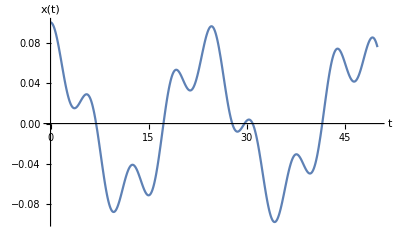

```mathematica
Plot[ q[[1]]/. solution[t] , { t, 0, 50 } , AxesLabel-> { t, q[[1]] } ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]  ,
{ tmax , 0.01 , 300  } ]
```

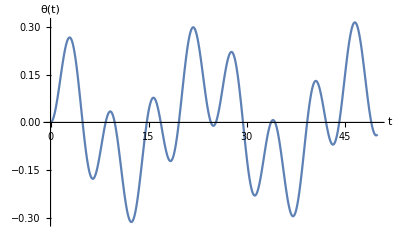

```mathematica
Plot[ q[[2]]/. solution[t] , { t, 0, 50 } , AxesLabel-> { t, q[[2]] }]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[2,2]] , solution'[t][[2,2]] } , { t , 0, tmax } , AxesLabel-> { q[[2]] , D[q[[2]], t] } ]  ,
{ tmax , 0.01 , 300 } ]
```